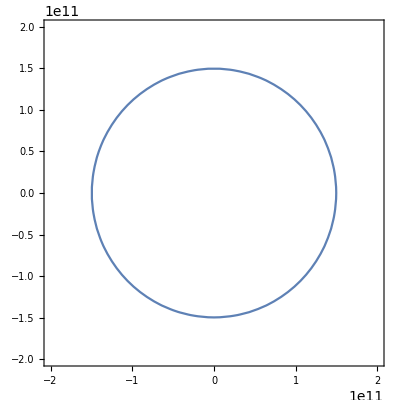

```mathematica
ContourPlot[x^2/((149576999.826*10^3)^2)+y^2/((149597887.5*10^3)^2)==1,{x,-2*10^8*10^3,2*10^8*10^3},{y,-2*10^8*10^3,2*10^8*10^3},Axes->True]
```

```mathematica
Clear["`*"]
```

```mathematica
ContourPlot3D[((z)^2+(x×Cos[7.25°×Pi/(180°)])^2)/((149576999.826*10^3)^2)+(y)^2/((149597887.5*10^3)^2)==1,{x,-2*10^11,2*10^11},{y,-2*10^11,2*10^11},{z,-2.5*10^11,2.5*10^11}]
```

```mathematica
A=ContourPlot3D[((z)^2+(x×Cos[7.25°×Pi/(180°)])^2)/((149576999.826*10^3)^2)+(y)^2/((149597887.5*10^3)^2)==1,{x,-2*10^11,2*10^11},{y,-2*10^11,2*10^11},{z,-2.5*10^11,2.5*10^11}];
B=ContourPlot3D[z==x*Sin[7.25°×Pi/(180°)],{x,-2*10^11,2*10^11},{y,-2*10^11,2*10^11},{z,-2.5*10^11,2.5*10^11}];
Show[A,B]
RegionPlot3D[RegionIntersection[A,B],{x,-2*10^11,2*10^11},{y,-2*10^11,2*10^11},{z,-2.5*10^11,2.5*10^11}]
```